```mathematica
$PlotTheme="Scientific";
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};DefaultBaseStyle->texStyle;
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
k1v={k1,0,0};
```

```mathematica
k2v={k2*cth,k2*√(1-cth^2),0};
```

```mathematica
k0v={k0*cpsi,k0*√(1-cpsi^2)*Cos[ϕ],k0*√(1-cpsi^2)*Sin[ϕ]};
```

```mathematica
term=FullSimplify[((k0v+k1v).k2v*((k0v-k2v).(k0v-k2v)-(k0v+k1v).(k0v+k1v)))/((k0v+k1v).(k0v+k1v)*(k1v+k2v).(k1v+k2v))]
```

-(k2 (cth (cpsi k0+k1)+√(1-cpsi^2) √(1-cth^2) k0 Cos[ϕ]) (k1^2-k2^2+2 cpsi k0 (k1+cth k2)+2 √(1-cpsi^2) √(1-cth^2) k0 k2 Cos[ϕ]))/((k0^2+2 cpsi k0 k1+k1^2) (k1^2+2 cth k1 k2+k2^2))

```mathematica
inter[r_]:=Module[{int,errors},int=Chop[NIntegrate[Boole[(k1^2+k2^2+2*k1*k2*cth≤1)&&(k1^2+k0^2+2*k1*k0*cpsi≤1)]*k0*k1^2*r*Sin[r*k0]*term,{k1,0,2},{k2,0,1},{k0,0,3},{ϕ,0,2*π},{cth,-1,1},{cpsi,-1,1},PrecisionGoal->5,(*WorkingPrecision->15,*)IntegrationMonitor:>((errors=Through[#1@"Error"])&)]];
{{r,int/(16*π^2)},Re[Total@errors]/(16*π^2),Abs[Re[Total@errors]/Re[int]]}]
```

```mathematica
taberr=<<"2017-05-30 New distribution over space 20ths.m";
```

```mathematica
(*taberr={};Monitor[For[r=1/20,r≤15,r=r+1/20,taberr=Join[taberr,{inter[r]}]]
,taberr//MatrixForm//ScientificForm];taberr//MatrixForm//ScientificForm*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.41854×10^-6 and 0.000012976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000188906 and 0.0000515568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000908956 and 0.000115582 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

({1/20,-8.98303×10^-9} | 8.21712×10^-8 | 9.14738
{1/10,-1.19626×10^-7} | 3.26487×10^-7 | 2.72924
{3/20,-5.75603×10^-7} | 7.31934×10^-7 | 1.27159
{1/5,-1.77397×10^-6} | 1.29984×10^-6 | 7.32731×10^-1
{1/4,-4.26322×10^-6} | 2.01342×10^-6 | 4.72278×10^-1
{3/10,-8.73724×10^-6} | 2.90232×10^-6 | 3.32178×10^-1
{7/20,-1.60129×10^-5} | 3.94831×10^-6 | 2.4657×10^-1
{2/5,-2.70063×10^-5} | 5.10928×10^-6 | 1.89189×10^-1
{9/20,-4.2724×10^-5} | 6.40126×10^-6 | 1.49828×10^-1
{1/2,-6.47494×10^-5} | 7.74404×10^-6 | 1.196×10^-1
{11/20,-9.28134×10^-5} | 9.58767×10^-6 | 1.033×10^-1
{3/5,-1.29527×10^-4} | 1.11956×10^-5 | 8.64351×10^-2
{13/20,-1.75374×10^-4} | 1.30906×10^-5 | 7.46439×10^-2
{7/10,-2.31862×10^-4} | 1.51874×10^-5 | 6.55018×10^-2
{3/4,-2.99803×10^-4} | 1.70159×10^-5 | 5.67568×10^-2
{4/5,-3.8147×10^-4} | 1.77962×10^-5 | 4.66517×10^-2
{17/20,-4.7469×10^-4} | 2.07858×10^-5 | 4.37881×10^-2
{9/10,-5.8568×10^-4} | 2.22836×10^-5 | 3.80475×10^-2
{19/20,-7.09459×10^-4} | 2.39674×10^-5 | 3.37826×10^-2
{1,-8.49064×10^-4} | 2.64495×10^-5 | 3.11514×10^-2
{21/20,-9.97591×10^-4} | 2.74422×10^-5 | 2.75085×10^-2
{11/10,-1.1725×10^-3} | 3.12762×10^-5 | 2.66748×10^-2
{23/20,-1.35861×10^-3} | 3.42142×10^-5 | 2.51832×10^-2
{6/5,-1.56203×10^-3} | 3.68096×10^-5 | 2.35653×10^-2
{5/4,-1.77957×10^-3} | 3.86299×10^-5 | 2.17075×10^-2
{13/10,-2.01304×10^-3} | 4.08612×10^-5 | 2.02982×10^-2
{27/20,-2.26006×10^-3} | 4.2599×10^-5 | 1.88486×10^-2
{7/5,-2.51807×10^-3} | 4.69239×10^-5 | 1.86348×10^-2
{29/20,-2.78708×10^-3} | 4.82393×10^-5 | 1.73082×10^-2
{3/2,-3.06546×10^-3} | 5.01736×10^-5 | 1.63674×10^-2
{31/20,-3.35216×10^-3} | 5.14368×10^-5 | 1.53444×10^-2
{8/5,-3.643×10^-3} | 5.35267×10^-5 | 1.4693×10^-2
{33/20,-3.93799×10^-3} | 5.67695×10^-5 | 1.44159×10^-2
{17/10,-4.23138×10^-3} | 5.77166×10^-5 | 1.36401×10^-2
{7/4,-4.51469×10^-3} | 5.42187×10^-5 | 1.20094×10^-2
{9/5,-4.81621×10^-3} | 6.48278×10^-5 | 1.34603×10^-2
{37/20,-5.10117×10^-3} | 6.34569×10^-5 | 1.24397×10^-2
{19/10,-5.3744×10^-3} | 6.52686×10^-5 | 1.21443×10^-2
{39/20,-5.63304×10^-3} | 6.63841×10^-5 | 1.17848×10^-2
{2,-5.87714×10^-3} | 6.81017×10^-5 | 1.15876×10^-2
{41/20,-6.10587×10^-3} | 7.10943×10^-5 | 1.16436×10^-2
{21/10,-6.31491×10^-3} | 7.29026×10^-5 | 1.15445×10^-2
{43/20,-6.50571×10^-3} | 7.33855×10^-5 | 1.12802×10^-2
{11/5,-6.66754×10^-3} | 7.4851×10^-5 | 1.12262×10^-2
{9/4,-6.80782×10^-3} | 7.47173×10^-5 | 1.09752×10^-2
{23/10,-6.90474×10^-3} | 7.9234×10^-5 | 1.14753×10^-2
{47/20,-6.97849×10^-3} | 7.93323×10^-5 | 1.13681×10^-2
{12/5,-7.01934×10^-3} | 8.10023×10^-5 | 1.15399×10^-2
{49/20,-7.02919×10^-3} | 7.92613×10^-5 | 1.1276×10^-2
{5/2,-6.99984×10^-3} | 8.17803×10^-5 | 1.16832×10^-2
{51/20,-6.93525×10^-3} | 8.73625×10^-5 | 1.25969×10^-2
{13/5,-6.83689×10^-3} | 8.64407×10^-5 | 1.26433×10^-2
{53/20,-6.70106×10^-3} | 9.21348×10^-5 | 1.37493×10^-2
{27/10,-6.52982×10^-3} | 9.18106×10^-5 | 1.40602×10^-2
{11/4,-6.32536×10^-3} | 8.7631×10^-5 | 1.38539×10^-2
{14/5,-6.0684×10^-3} | 8.83372×10^-5 | 1.45569×10^-2
{57/20,-5.79678×10^-3} | 9.75674×10^-5 | 1.68313×10^-2
{29/10,-5.49231×10^-3} | 9.86254×10^-5 | 1.7957×10^-2
{59/20,-5.15503×10^-3} | 9.90038×10^-5 | 1.92053×10^-2
{3,-4.78248×10^-3} | 1.02388×10^-4 | 2.1409×10^-2
{61/20,-4.37941×10^-3} | 1.06088×10^-4 | 2.42244×10^-2
{31/10,-3.96203×10^-3} | 1.06012×10^-4 | 2.67569×10^-2
{63/20,-3.5176×10^-3} | 1.1152×10^-4 | 3.17033×10^-2
{16/5,-3.07052×10^-3} | 1.1365×10^-4 | 3.70134×10^-2
{13/4,-2.58092×10^-3} | 1.13894×10^-4 | 4.41294×10^-2
{33/10,-2.08304×10^-3} | 1.12575×10^-4 | 5.40439×10^-2
{67/20,-1.58219×10^-3} | 1.11757×10^-4 | 7.06346×10^-2
{17/5,-1.08267×10^-3} | 1.13892×10^-4 | 1.05196×10^-1
{69/20,-5.73644×10^-4} | 1.12152×10^-4 | 1.95508×10^-1
{7/2,-6.12346×10^-5} | 1.18448×10^-4 | 1.93433
{71/20,4.51404×10^-4} | 1.20798×10^-4 | 2.67604×10^-1
{18/5,9.48203×10^-4} | 1.23396×10^-4 | 1.30137×10^-1
{73/20,1.44196×10^-3} | 1.27057×10^-4 | 8.81141×10^-2
{37/10,1.91987×10^-3} | 1.23332×10^-4 | 6.424×10^-2
{15/4,2.38751×10^-3} | 1.21547×10^-4 | 5.09092×10^-2
{19/5,2.84041×10^-3} | 1.21808×10^-4 | 4.28842×10^-2
{77/20,3.27461×10^-3} | 1.224×10^-4 | 3.73786×10^-2
{39/10,3.66871×10^-3} | 1.31085×10^-4 | 3.57306×10^-2
{79/20,4.05833×10^-3} | 1.22979×10^-4 | 3.03029×10^-2
{4,4.41134×10^-3} | 1.29813×10^-4 | 2.94271×10^-2
{81/20,4.73987×10^-3} | 1.31246×10^-4 | 2.76897×10^-2
{41/10,5.03955×10^-3} | 1.38105×10^-4 | 2.74042×10^-2
{83/20,5.32231×10^-3} | 1.40513×10^-4 | 2.64007×10^-2
{21/5,5.55646×10^-3} | 1.42123×10^-4 | 2.55779×10^-2
{17/4,5.76749×10^-3} | 1.42643×10^-4 | 2.47323×10^-2
{43/10,5.94993×10^-3} | 1.50761×10^-4 | 2.53384×10^-2
{87/20,6.09897×10^-3} | 1.47178×10^-4 | 2.41317×10^-2
{22/5,6.20297×10^-3} | 1.49093×10^-4 | 2.40357×10^-2
{89/20,6.29065×10^-3} | 1.50137×10^-4 | 2.38666×10^-2
{9/2,6.33419×10^-3} | 1.50389×10^-4 | 2.37424×10^-2
{91/20,6.3681×10^-3} | 1.54749×10^-4 | 2.43006×10^-2
{23/5,6.36386×10^-3} | 1.57101×10^-4 | 2.46865×10^-2
{93/20,6.3359×10^-3} | 1.62877×10^-4 | 2.5707×10^-2
{47/10,6.28782×10^-3} | 1.61245×10^-4 | 2.56441×10^-2
{19/4,6.20258×10^-3} | 1.63414×10^-4 | 2.63462×10^-2
{24/5,6.11201×10^-3} | 1.59785×10^-4 | 2.61428×10^-2
{97/20,5.98384×10^-3} | 1.72838×10^-4 | 2.88841×10^-2
{49/10,5.83613×10^-3} | 1.79804×10^-4 | 3.08087×10^-2
{99/20,5.68029×10^-3} | 1.79341×10^-4 | 3.15726×10^-2
{5,5.5085×10^-3} | 1.79966×10^-4 | 3.26706×10^-2
{101/20,5.32322×10^-3} | 1.76312×10^-4 | 3.31213×10^-2
{51/10,5.12697×10^-3} | 1.71722×10^-4 | 3.34939×10^-2
{103/20,4.91588×10^-3} | 1.91587×10^-4 | 3.89731×10^-2
{26/5,4.69908×10^-3} | 1.93004×10^-4 | 4.10727×10^-2
{21/4,4.48722×10^-3} | 1.8898×10^-4 | 4.21152×10^-2
{53/10,4.26695×10^-3} | 1.93356×10^-4 | 4.53147×10^-2
{107/20,4.03463×10^-3} | 1.97093×10^-4 | 4.88502×10^-2
{27/5,3.815×10^-3} | 1.9871×10^-4 | 5.20864×10^-2
{109/20,3.58141×10^-3} | 1.99209×10^-4 | 5.56231×10^-2
{11/2,3.35988×10^-3} | 1.96793×10^-4 | 5.85715×10^-2
{111/20,3.14808×10^-3} | 2.03741×10^-4 | 6.47191×10^-2
{28/5,2.93564×10^-3} | 2.00927×10^-4 | 6.84441×10^-2
{113/20,2.74533×10^-3} | 1.98397×10^-4 | 7.22671×10^-2
{57/10,2.52489×10^-3} | 1.99749×10^-4 | 7.9112×10^-2
{23/4,2.33151×10^-3} | 2.07459×10^-4 | 8.89804×10^-2
{29/5,2.14795×10^-3} | 2.0364×10^-4 | 9.48069×10^-2
{117/20,1.94911×10^-3} | 2.00812×10^-4 | 1.03028×10^-1
{59/10,1.79479×10^-3} | 2.11198×10^-4 | 1.17673×10^-1
{119/20,1.63325×10^-3} | 2.13596×10^-4 | 1.3078×10^-1
{6,1.48333×10^-3} | 2.23851×10^-4 | 1.50911×10^-1
{121/20,1.33735×10^-3} | 2.22687×10^-4 | 1.66514×10^-1
{61/10,1.2065×10^-3} | 2.30847×10^-4 | 1.91337×10^-1
{123/20,1.05669×10^-3} | 2.34706×10^-4 | 2.22113×10^-1
{31/5,1.04367×10^-3} | 2.22284×10^-4 | 2.12983×10^-1
{25/4,8.66713×10^-4} | 2.55736×10^-4 | 2.95064×10^-1
{63/10,7.76711×10^-4} | 2.54745×10^-4 | 3.27979×10^-1
{127/20,6.80589×10^-4} | 2.57002×10^-4 | 3.77618×10^-1
{32/5,6.04923×10^-4} | 2.63226×10^-4 | 4.3514×10^-1
{129/20,5.40501×10^-4} | 2.67915×10^-4 | 4.9568×10^-1
{13/2,4.7788×10^-4} | 2.79898×10^-4 | 5.85708×10^-1
{131/20,3.98225×10^-4} | 2.62662×10^-4 | 6.59582×10^-1
{33/5,3.35694×10^-4} | 2.73751×10^-4 | 8.15478×10^-1
{133/20,3.01661×10^-4} | 2.83351×10^-4 | 9.39302×10^-1
{67/10,2.56992×10^-4} | 2.80354×10^-4 | 1.0909
{27/4,2.22678×10^-4} | 2.75785×10^-4 | 1.23849
{34/5,1.62774×10^-4} | 2.69313×10^-4 | 1.65452
{137/20,1.63138×10^-4} | 2.74271×10^-4 | 1.68122
{69/10,1.50334×10^-4} | 2.79814×10^-4 | 1.86128
{139/20,1.21083×10^-4} | 2.84591×10^-4 | 2.35038
{7,1.04721×10^-4} | 2.92841×10^-4 | 2.79639
{141/20,8.87537×10^-5} | 2.89206×10^-4 | 3.25852
{71/10,9.26731×10^-5} | 3.01603×10^-4 | 3.25448
{143/20,5.64852×10^-5} | 3.14889×10^-4 | 5.57472
{36/5,5.04774×10^-5} | 3.09478×10^-4 | 6.13102
{29/4,6.21813×10^-5} | 2.97278×10^-4 | 4.78083
{73/10,3.66003×10^-5} | 2.98097×10^-4 | 8.14465
{147/20,2.13068×10^-5} | 3.13433×10^-4 | 1.47105×10^1
{37/5,2.69979×10^-5} | 3.25755×10^-4 | 1.2066×10^1
{149/20,1.7919×10^-5} | 3.17489×10^-4 | 1.7718×10^1
{15/2,1.82001×10^-5} | 3.12031×10^-4 | 1.71444×10^1
{151/20,2.60071×10^-5} | 3.1442×10^-4 | 1.20898×10^1
{38/5,2.51251×10^-6} | 3.36966×10^-4 | 1.34115×10^2
{153/20,-2.87437×10^-5} | 3.19139×10^-4 | 1.11029×10^1
{77/10,-7.45479×10^-6} | 3.35181×10^-4 | 4.49618×10^1
{31/4,2.22774×10^-5} | 3.48878×10^-4 | 1.56607×10^1
{39/5,3.31274×10^-5} | 3.5069×10^-4 | 1.05861×10^1
{157/20,1.00727×10^-5} | 3.49858×10^-4 | 3.47332×10^1
{79/10,4.58356×10^-6} | 3.57393×10^-4 | 7.79728×10^1
{159/20,1.86482×10^-5} | 3.40883×10^-4 | 1.82796×10^1
{8,1.03313×10^-5} | 3.47648×10^-4 | 3.36499×10^1
{161/20,-7.83289×10^-6} | 3.65271×10^-4 | 4.6633×10^1
{81/10,-8.5046×10^-6} | 3.60217×10^-4 | 4.23556×10^1
{163/20,-2.32622×10^-5} | 3.61751×10^-4 | 1.5551×10^1
{41/5,-2.59773×10^-5} | 3.46862×10^-4 | 1.33525×10^1
{33/4,-1.63866×10^-5} | 3.54217×10^-4 | 2.16163×10^1
{83/10,-1.98724×10^-5} | 3.52119×10^-4 | 1.7719×10^1
{167/20,-2.27452×10^-5} | 3.71428×10^-4 | 1.633×10^1
{42/5,7.84181×10^-6} | 3.44343×10^-4 | 4.39112×10^1
{169/20,-3.4648×10^-5} | 3.51464×10^-4 | 1.01439×10^1
{17/2,-3.48006×10^-5} | 3.77397×10^-4 | 1.08446×10^1
{171/20,-5.64354×10^-5} | 3.91967×10^-4 | 6.94542
{43/5,-3.57964×10^-5} | 3.9217×10^-4 | 1.09556×10^1
{173/20,-3.42831×10^-5} | 4.05556×10^-4 | 1.18296×10^1
{87/10,-4.0906×10^-5} | 4.11224×10^-4 | 1.00529×10^1
{35/4,-4.83271×10^-5} | 4.01908×10^-4 | 8.31641
{44/5,-5.3771×10^-5} | 3.90244×10^-4 | 7.25751
{177/20,-6.88855×10^-5} | 4.06731×10^-4 | 5.90445
{89/10,-9.3554×10^-5} | 4.07839×10^-4 | 4.35939
{179/20,-7.42302×10^-5} | 3.8666×10^-4 | 5.20894
{9,-1.11865×10^-4} | 4.19469×10^-4 | 3.74979
{181/20,-1.26585×10^-4} | 4.23577×10^-4 | 3.34619
{91/10,-1.23631×10^-4} | 4.40663×10^-4 | 3.56434
{183/20,-9.61324×10^-5} | 4.52815×10^-4 | 4.71033
{46/5,-1.00872×10^-4} | 4.54336×10^-4 | 4.50407
{37/4,-1.08808×10^-4} | 4.70577×10^-4 | 4.32485
{93/10,-1.11608×10^-4} | 4.59283×10^-4 | 4.11515
{187/20,-1.06177×10^-4} | 4.88658×10^-4 | 4.6023
{47/5,-1.20626×10^-4} | 4.84965×10^-4 | 4.0204
{189/20,-1.02819×10^-4} | 4.94968×10^-4 | 4.81398
{19/2,-1.08057×10^-4} | 5.11174×10^-4 | 4.73059
{191/20,-1.14939×10^-4} | 5.00793×10^-4 | 4.35702
{48/5,-1.04043×10^-4} | 4.75066×10^-4 | 4.56603
{193/20,-1.2931×10^-4} | 4.84315×10^-4 | 3.74539
{97/10,-7.01968×10^-5} | 4.78647×10^-4 | 6.81864
{39/4,-1.31708×10^-4} | 4.97193×10^-4 | 3.77497
{49/5,-1.48205×10^-4} | 4.9886×10^-4 | 3.36602
{197/20,-1.30206×10^-4} | 5.00912×10^-4 | 3.84706
{99/10,-1.04818×10^-4} | 4.71467×10^-4 | 4.49798
{199/20,-1.2794×10^-4} | 5.12051×10^-4 | 4.00228
{10,-1.15884×10^-4} | 5.06369×10^-4 | 4.36963
{201/20,-1.11694×10^-4} | 5.11016×10^-4 | 4.57516
{101/10,-1.17467×10^-4} | 5.15608×10^-4 | 4.38937
{203/20,-9.00706×10^-5} | 5.324×10^-4 | 5.91092
{51/5,-1.06488×10^-4} | 5.35157×10^-4 | 5.0255
{41/4,-8.79979×10^-5} | 5.48449×10^-4 | 6.23252
{103/10,-4.30013×10^-5} | 5.36813×10^-4 | 1.24836×10^1
{207/20,-4.98908×10^-5} | 5.26302×10^-4 | 1.05491×10^1
{52/5,-3.25682×10^-5} | 5.12833×10^-4 | 1.57464×10^1
{209/20,-8.82134×10^-5} | 5.17302×10^-4 | 5.86422
{21/2,-4.79758×10^-5} | 5.66567×10^-4 | 1.18094×10^1
{211/20,-3.13967×10^-5} | 5.62027×10^-4 | 1.79008×10^1
{53/5,-1.5039×10^-5} | 5.74063×10^-4 | 3.81716×10^1
{213/20,-1.97119×10^-5} | 5.83082×10^-4 | 2.95802×10^1
{107/10,-1.24393×10^-5} | 5.88965×10^-4 | 4.73472×10^1
{43/4,8.36559×10^-7} | 5.40881×10^-4 | 6.46554×10^2
{54/5,3.77867×10^-5} | 5.52609×10^-4 | 1.46244×10^1
{217/20,5.73377×10^-5} | 5.48545×10^-4 | 9.56693
{109/10,2.33545×10^-5} | 5.51319×10^-4 | 2.36066×10^1
{219/20,6.50814×10^-4} | 5.08988×10^-4 | 7.82079×10^-1
{11,8.39541×10^-5} | 5.9688×10^-4 | 7.1096
{221/20,1.07562×10^-4} | 5.83053×10^-4 | 5.42064
{111/10,1.19155×10^-4} | 5.93467×10^-4 | 4.98064
{223/20,1.09612×10^-4} | 5.8817×10^-4 | 5.36595
{56/5,1.05704×10^-4} | 5.8811×10^-4 | 5.56376
{45/4,1.07919×10^-4} | 5.91824×10^-4 | 5.48395
{113/10,1.54951×10^-4} | 5.93262×10^-4 | 3.82872
{227/20,1.23088×10^-4} | 5.87299×10^-4 | 4.77136
{57/5,1.12876×10^-4} | 6.08687×10^-4 | 5.39251
{229/20,1.20639×10^-4} | 6.28278×10^-4 | 5.2079
{23/2,1.32307×10^-4} | 6.43169×10^-4 | 4.86119
{231/20,1.0366×10^-4} | 6.1632×10^-4 | 5.94562
{58/5,1.25287×10^-4} | 6.15469×10^-4 | 4.91247
{233/20,1.20018×10^-4} | 6.34127×10^-4 | 5.2836
{117/10,1.14727×10^-4} | 6.55839×10^-4 | 5.71654
{47/4,1.36508×10^-4} | 6.44155×10^-4 | 4.7188
{59/5,1.13862×10^-4} | 6.67968×10^-4 | 5.86646
{237/20,1.17889×10^-4} | 6.61973×10^-4 | 5.61524
{119/10,1.41098×10^-4} | 6.38894×10^-4 | 4.52803
{239/20,1.09695×10^-4} | 6.20069×10^-4 | 5.65267
{12,9.88898×10^-5} | 6.33769×10^-4 | 6.40883
{241/20,1.01909×10^-4} | 6.96229×10^-4 | 6.83186
{121/10,1.36707×10^-4} | 6.77753×10^-4 | 4.95772
{243/20,1.10186×10^-4} | 7.43808×10^-4 | 6.75048
{61/5,7.56974×10^-5} | 7.2802×10^-4 | 9.61751
{49/4,7.97392×10^-5} | 7.20432×10^-4 | 9.03485
{123/10,9.60926×10^-5} | 7.13048×10^-4 | 7.42043
{247/20,9.65707×10^-5} | 7.26678×10^-4 | 7.52483
{62/5,1.26118×10^-4} | 7.08146×10^-4 | 5.61495
{249/20,4.7571×10^-5} | 7.11408×10^-4 | 1.49547×10^1
{25/2,7.40573×10^-5} | 6.9816×10^-4 | 9.4273
{251/20,9.43289×10^-5} | 7.33095×10^-4 | 7.77169
{63/5,5.645×10^-5} | 6.96821×10^-4 | 1.2344×10^1
{253/20,2.84947×10^-5} | 6.74902×10^-4 | 2.36852×10^1
{127/10,5.35691×10^-5} | 7.30649×10^-4 | 1.36394×10^1
{51/4,6.18069×10^-5} | 7.62312×10^-4 | 1.23338×10^1
{64/5,2.4283×10^-5} | 7.18114×10^-4 | 2.95727×10^1
{257/20,4.31432×10^-5} | 7.64386×10^-4 | 1.77174×10^1
{129/10,1.13859×10^-4} | 7.53688×10^-4 | 6.6195
{259/20,4.68887×10^-5} | 7.60147×10^-4 | 1.62117×10^1
{13,1.91995×10^-5} | 7.89753×10^-4 | 4.1134×10^1
{261/20,8.9914×10^-5} | 8.01442×10^-4 | 8.91343
{131/10,6.47649×10^-5} | 7.74541×10^-4 | 1.19593×10^1
{263/20,4.47565×10^-5} | 8.33597×10^-4 | 1.86252×10^1
{66/5,-8.70144×10^-7} | 8.03707×10^-4 | 9.23648×10^2
{53/4,3.24157×10^-5} | 8.12578×10^-4 | 2.50674×10^1
{133/10,1.02251×10^-5} | 8.29004×10^-4 | 8.1075×10^1
{267/20,4.04745×10^-5} | 8.06886×10^-4 | 1.99357×10^1
{67/5,2.19138×10^-5} | 7.80757×10^-4 | 3.56285×10^1
{269/20,8.06432×10^-5} | 8.06234×10^-4 | 9.99753
{27/2,2.39827×10^-5} | 8.24483×10^-4 | 3.43782×10^1
{271/20,3.34595×10^-5} | 8.01179×10^-4 | 2.39447×10^1
{68/5,5.19389×10^-5} | 8.10474×10^-4 | 1.56044×10^1
{273/20,-2.60505×10^-5} | 8.15544×10^-4 | 3.13063×10^1
{137/10,-1.19545×10^-5} | 8.32321×10^-4 | 6.96243×10^1
{55/4,-2.53467×10^-5} | 8.35202×10^-4 | 3.29511×10^1
{69/5,6.78057×10^-6} | 8.23814×10^-4 | 1.21496×10^2
{277/20,-2.14727×10^-5} | 8.59239×10^-4 | 4.00154×10^1
{139/10,-1.02159×10^-5} | 8.95532×10^-4 | 8.76603×10^1
{279/20,1.2331×10^-8} | 8.91035×10^-4 | 7.22597×10^4
{14,-6.06183×10^-6} | 9.1048×10^-4 | 1.50199×10^2
{281/20,-4.80899×10^-6} | 8.86523×10^-4 | 1.84347×10^2
{141/10,-3.4602×10^-5} | 9.39553×10^-4 | 2.71531×10^1
{283/20,-3.12942×10^-5} | 8.39666×10^-4 | 2.68314×10^1
{71/5,-1.12403×10^-5} | 8.66963×10^-4 | 7.71296×10^1
{57/4,-3.03658×10^-5} | 9.03266×10^-4 | 2.97462×10^1
{143/10,2.13592×10^-5} | 9.30663×10^-4 | 4.35721×10^1
{287/20,-7.1109×10^-6} | 9.48334×10^-4 | 1.33363×10^2
{72/5,1.55412×10^-5} | 9.50598×10^-4 | 6.11664×10^1
{289/20,4.30396×10^-6} | 9.40432×10^-4 | 2.18504×10^2
{29/2,-5.6735×10^-6} | 9.94521×10^-4 | 1.75292×10^2
{291/20,2.96384×10^-5} | 1.00044×10^-3 | 3.3755×10^1
{73/5,4.33075×10^-5} | 1.01701×10^-3 | 2.34836×10^1
{293/20,-1.547×10^-5} | 1.01736×10^-3 | 6.57636×10^1
{147/10,-2.53734×10^-5} | 9.69152×10^-4 | 3.81956×10^1
{59/4,-4.59737×10^-5} | 9.96729×10^-4 | 2.16804×10^1
{74/5,4.63913×10^-5} | 1.01718×10^-3 | 2.19262×10^1
{297/20,-1.6341×10^-5} | 9.81424×10^-4 | 6.00592×10^1
{149/10,-3.22618×10^-5} | 9.80598×10^-4 | 3.0395×10^1
{299/20,-4.0404×10^-6} | 9.25845×10^-4 | 2.29147×10^2
{15,-2.45152×10^-5} | 1.0272×10^-3 | 4.19005×10^1)

```mathematica
figscgr20ths=ErrorListPlot[Table[{taberr[[n,1]],ErrorBar[taberr[[n,2]]]},{n,1,Length[taberr]}],GridLines->{{0,3.5,7,8},{0}},PlotRange->Full,PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{acg}}^\\circ\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}],Epilog->{Inset[Text[MaTeX["\\text{Core}",Magnification->1.25]],{2.25,-0.002}],Inset[Text[MaTeX["\\text{Halo}",Magnification->1.25]],{4.75,0.002}]}]
```

-Graphics-

The following confirms that the core and halo balance

```mathematica
taberr[[7*20]]
```

{{7,0.000104721},0.000292841,2.79639}

```mathematica
ScientificForm[Total[Take[Transpose[Transpose[taberr][[1]]][[2]],7*20]]*1/20,3]
```

-2.22×10^-5

```mathematica
ScientificForm[Total[Take[Transpose[Transpose[taberr][[1]]][[2]],8*20]]*1/20,3]
```

5.93×10^-6

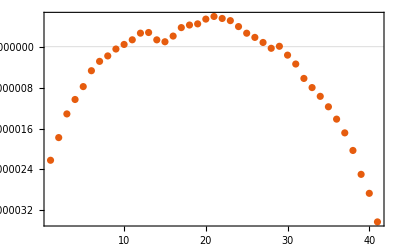

```mathematica
ListPlot[Table[Total[Take[Transpose[Transpose[taberr][[1]]][[2]],n]]*1/20,{n,8*20-20,8*20+20}],PlotRange->Full]
```

```mathematica
ScientificForm[Total[Take[Transpose[Transpose[taberr][[1]]][[2]],8*20-5]]*1/20,3]
```

2.1×10^-6

The following confirms that overall from r=0 to 15 there is good balance

```mathematica
ScientificForm[Total[Transpose[Transpose[taberr][[1]]][[2]]]*1/20,3]
```

5.82×10^-5

```mathematica
ft={{-1/10000,"-10 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{-1/20000,"-5 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{-3/10000,"-15 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{3/100000,"",{0.005,0}},{1/50000,"",{0.005,0}},{1/100000,"",{0.005,0}},{0,"",{0.005,0}},{-1/100000,"",{0.005,0}},{-1/50000,"",{0.005,0}},{0,"0"},{-3/100000,"",{0.005,0}},{-1/25000,"",{0.005,0}},{-1/20000,"",{0.005,0}},{-3/50000,"",{0.005,0}},{-7/100000,"",{0.005,0}},{-1/12500,"",{0.005,0}},{-9/100000,"",{0.005,0}},{-1/10000,"",{0.005,0}},{-11/100000,"",{0.005,0}},{-3/25000,"",{0.005,0}},{-13/100000,"",{0.005,0}},{-7/50000,"",{0.005,0}},{-3/20000,"",{0.005,0}}};
```

```mathematica
figscgr20thsdensity=ErrorListPlot[Table[{{taberr[[n,1,1]],taberr[[n,1,2]]/(4*π*taberr[[n,1,1]]^2)},ErrorBar[taberr[[n,2]]/(4*π*taberr[[n,1,1]]^2)]},{n,1,Length[taberr]}],GridLines->{{0,3.5,7},{0}},(*GridLinesStyle->Directive[Gray],*)PlotRange->{{Automatic,8},Full},PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\frac{\\hat{S}_{\\text{acg}}^\\circ\\left(k_{\\text{J}}\\beta\\, r\\right)}{4\\pi \\left(k_{\\text{J}}\\beta\\, r\\right)^2}",Magnification->1.25]},RotateLabel->False,FrameTicks->{{ft,None},{Automatic,None}},ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}],Epilog->{Inset[Text[MaTeX["\\text{Core}",Magnification->1.25]],{1.75,-0.00004}],Inset[Text[MaTeX["\\text{Halo}",Magnification->1.25]],{4.4,0.00001}]}]
```

-Graphics-

```mathematica
Export["figscgr20ths.pdf",figscgr20ths,ImageResolution->1000];
```

```mathematica
Export["figscgr20thsdensity.pdf",figscgr20thsdensity,ImageResolution->1000];
```

```mathematica
(*Export["2017-05-30 New distribution over space 20ths.m",taberr]*)
```